```mathematica
importDir ="/home/gillen/Documents/Computation/saved_outputs/2D_Polar/Twist:0-180/Time_step:2.500000e-03__frames:50__Date:14-Oct-2015 13:01:42/";
nMatrix= Import[(*importDir<>*) "n2d.mat"]⟦1⟧;
(*avgEnergy = Import[importDir <> "avgEnergy.mat"]⟦1⟧;*)
```

```mathematica
(*This is real janky, let me know if there's a better way to imbed data into a notebook
```

```mathematica
(*Manipulate[ListVectorPlot[XYMatrix⟦frame,;;,;;⟧,VectorStyle-> Arrowheads[0],VectorPoints->All],{frame,1,frames,1}]*)
```

```mathematica
(*Manipulate[ListDensityPlot[Sin[θMatrix⟦frame⟧]^2 ᵀ,ColorFunctionScaling->False,ColorFunction->GrayLevel],{frame,1,frames,1}]*)
```

```mathematica
Dimensions@nMatrix;
(*nMatrix=Transpose[nMatrix,{1,4,2,3}];*)
{frames,ϕ}=Dimensions[nMatrix]⟦;;-2⟧
(*θMatrix=ArcTan[nMatrix⟦;;,;;,;;,1⟧,nMatrix⟦;;,;;,;;,2⟧];*)
θMatrix=nMatrix⟦;;,;;,;;⟧;
XYMatrix= Through[{Cos, Sin}[nMatrix]];
XYMatrix = Transpose[XYMatrix, {4,1,3,2}];
Dimensions@XYMatrix
```

{100,10}

{100,10,10,2}

```mathematica
Quiet@Manipulate[ListVectorPlot[XYMatrix⟦frame,;;,;;⟧,VectorPoints->All,PlotLabel->"Director Map 200 μm Cell Size", PlotTheme->"Monochrome",FrameTicks->None],{frame,1,100,1}]
```

```mathematica
ListPlot[avgEnergy, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```

ListPlot::lpn: avgEnergy is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[avgEnergy,PlotRange→All,PlotTheme→Monochrome,PlotMarkers→Automatic,Joined→True,InterpolationOrder→1,Frame→True,Axes→True,FrameLabel→{Time, but in dumb units,Average Energy (J)},PlotLabel→Average Energy of Directors Over Time]

```mathematica
t = Range[0,(2.5*^-3)*49,2.5*^-3]
```

{0.,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02,0.0225,0.025,0.0275,0.03,0.0325,0.035,0.0375,0.04,0.0425,0.045,0.0475,0.05,0.0525,0.055,0.0575,0.06,0.0625,0.065,0.0675,0.07,0.0725,0.075,0.0775,0.08,0.0825,0.085,0.0875,0.09,0.0925,0.095,0.0975,0.1,0.1025,0.105,0.1075,0.11,0.1125,0.115,0.1175,0.12,0.1225}

```mathematica
Energy = avgEnergy[[1,;;]];
```

Part::partd: Part specification avgEnergy ⟦ 1, 1 ;; All ⟧ is longer than depth of object.

```mathematica
data=Thread[t,Energy];
Dimensions[Energy]
Dimensions[t]
```

{3}

{50}

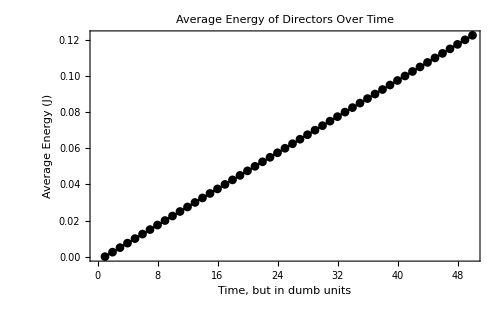

```mathematica
ListPlot[data, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```

```mathematica
data=Thread[Energy,t];
ListPlot[data, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```

ListPlot::lpn: avgEnergy ⟦ 1, 1 ;; All ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[avgEnergy⟦1,1;;All⟧,PlotRange→All,PlotTheme→Monochrome,PlotMarkers→Automatic,Joined→True,InterpolationOrder→1,Frame→True,Axes→True,FrameLabel→{Time, but in dumb units,Average Energy (J)},PlotLabel→Average Energy of Directors Over Time]